```mathematica
(* Placa Simplemente apoyada bajo carga puntual *)

(* Dimensiones de la placa *)
a=Input["Dimensión del lado x de la placa"];
b=Input["Dimensión del lado y de la placa"];
t=Input["Espesor de la placa de la placa"];
```

```mathematica
(* Parámetros mecánicos de la placa*)
ME=Input["Modulo de Elasticidad de la placa [kN/m2"];
poisson=Input["Modulo de Poisson de la placa"];
Dp=(ME t^3)/(12 (1-poisson^3));
```

```mathematica
(* Carga uniforme *)
P0=Input["Valor de la carga puntual [kN]"];
xp=Input["Posición x de la carga"];
yp=Input["Posición y de la carga"];
```

```mathematica
(* Valores de la suma  *)
vn=Input["Valor de n"];
vm=Input["Valor de m"];
```

```mathematica
(* Función de flecha para el caso de carga puntual *)
w[x_,y_]=(-4 P0/(a b Dp Pi^4))∑_(n=1)^vn ∑_(m=1)^vm (Sin[n Pi xp/a] Sin[m Pi yp/b](Sin[n Pi x/a] Sin[m Pi y/b])/ ((n/a)^2+(m/b)^2)^2);
```

```mathematica
(* Ploteado de la funcion de la flecha *)
(* Ploteado 3D *)
Plot3D[w[x,y],{x,0,a},{y,0,b}]
```

-Graphics3D-

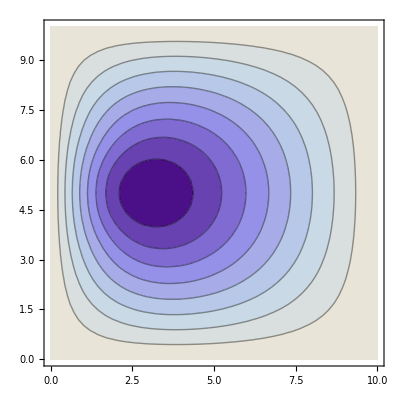

```mathematica
(* Curvas de Nivel*)
ContourPlot[w[x,y],{x,0,a},{y,0,b}]
```

```mathematica
(* Cálculo del Momento Mx *)
Mx[x_,y_]=-Dp (D[w[x,y], x,x]+poisson D[w[x,y], y,y]);
```

```mathematica
(* Ploteado 3D Mx *)
Plot3D[Mx[x,y],{x,0,a},{y,0,b}]
```

-Graphics3D-

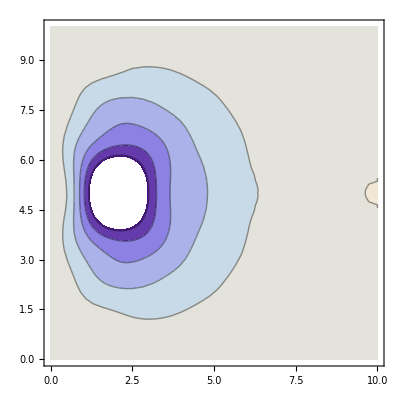

```mathematica
(* Curvas de Nivel Mx*) 
ContourPlot[Mx[x,y],{x,0,a},{y,0,b}]
```

```mathematica
(* Cálculo del Momento My *)
My[x_,y_]=-Dp (poisson  D[w[x,y], x,x]+ D[w[x,y], y,y]);
```

```mathematica
(* Ploteado 3D My *)
Plot3D[My[x,y],{x,0,a},{y,0,b}]
```

-Graphics3D-

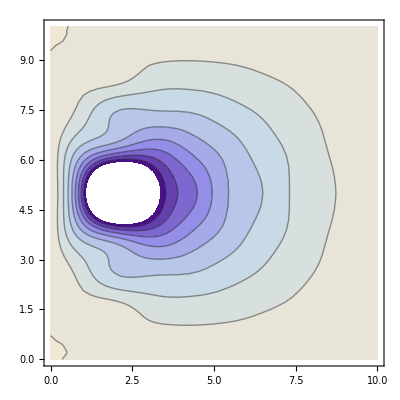

```mathematica
(* Curvas de Nivel Mx*) 
ContourPlot[My[x,y],{x,0,a},{y,0,b}]
```

```mathematica
(* Cálculo del Momento Mxy *)
Mxy[x_,y_]=-Dp ( D[w[x,y], x,y]);
```

```mathematica
(* Ploteado 3D My *)
Plot3D[Mxy[x,y],{x,0,a},{y,0,b}]
```

-Graphics3D-

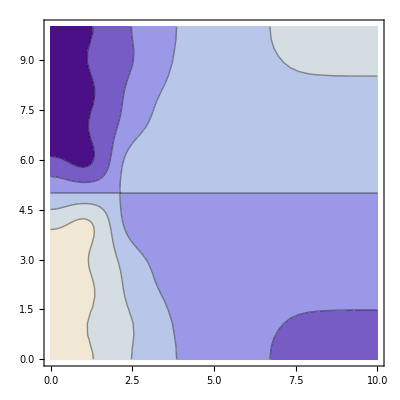

```mathematica
(* Curvas de Nivel Mx*) 
ContourPlot[Mxy[x,y],{x,0,a},{y,0,b}]
```

```mathematica
(* Cálculo de Qx *)
Qx[x_,y_]=-Dp  D[(D[w[x,y], x,x]+D[w[x,y], y,y]), x];
```

```mathematica
(* Ploteado 3D Qx *)
Plot3D[Qx[x,y],{x,0,a},{y,0,b}]
```

-Graphics3D-

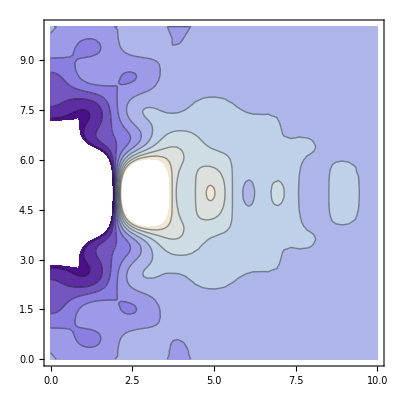

```mathematica
(* Cuevas de nivel 3D Qx *)
ContourPlot[Qx[x,y],{x,0,a},{y,0,b}]
```

```mathematica
(* Cálculo de Qy *)
Qy[x_,y_]=-Dp  D[(D[w[x,y], x,x]+D[w[x,y], y,y]), y];
```

```mathematica
(* Ploteado 3D Qy *)
Plot3D[Qy[x,y],{x,0,a},{y,0,b}]
```

-Graphics3D-

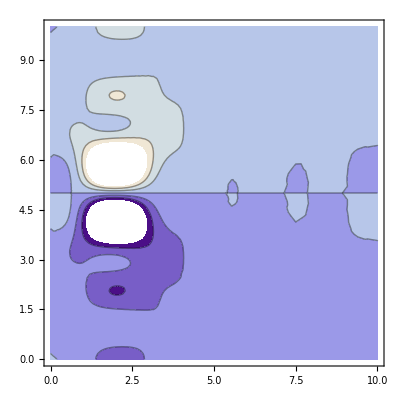

```mathematica
(* Cuevas de nivel 3D Qy *)
ContourPlot[Qy[x,y],{x,0,a},{y,0,b}]
```